# Section 1. The symbolic package

The symbolic package can be used to compute basis states and matrix elements as an analytic function of the number of color, Nc. In this section we will walk through the code in the symbolic package.
Since the symbolic computation is slow, we save a numerical version of the package, QCD-public.wl, where Nc takes a numerical value in the beginning to avoid symbolic computation, and we use QCD-public.wl to compute the QCD data to Δ_max=9. See the next section. The content of the symbolic package in this section is almost the same as the numerical package, QCD-public.wl.

## The package

```mathematica
ClearAll["Global`*"]
```

## Generate the basis states recursively

In this section, we generate the basis states at each dimension dim recursively from taking the double-trace construction of lower dim.

```mathematica
(* The coefficients in the double trace construction *)
PrimCoeffs[ΔA_,ΔB_,l_,k_]=((-1)^k Gamma[2ΔA+l]Gamma[2ΔB+l])/(k!(l-k)!Gamma[2ΔA+k]Gamma[2ΔB+l-k]);
```

stateSet[dim] computes the basis states at dimension dim from taking the double-trace construction of lower dim. 𝒪_1(∂^ℓ)^(<->)𝒪_2≡∑_k PrimCoeffs[Δ1,Δ2,ℓ,k] ∂^k 𝒪_1∂^(ℓ-k) 𝒪_2 
The output of stateSet[dim] is a list of operators written as
	{𝒪_1, 𝒪_2, ℓ, n, Δ }
where 𝒪_1 and 𝒪_2 are the two low dim operators that the operator is made of,
ℓ is the total number of derivatives acting on 𝒪_1 and 𝒪_2,
n is half of the total number of particles,
Δ is the total dimension, dim.
The beginning seed are operators ψ and ψ^†, represented by 1 and (-1), respectively.

```mathematica
ClearAll[stateSet]
stateSet[dim_]:=stateSet[dim]=DeleteDuplicatesBy[
Select[
Block[
{ set={} },
If[dim≥1,
(* There is always exactly one 2 particle state. *)
AppendTo[set, {-1,1,dim-1,1,dim}];
Do[
AppendTo[set,{state1,state2,dim-dim1-dim2,state1[[4]]+state2[[4]],dim}],
{dim1,dim-1,1,-1},
{dim2,1,Min[dim-dim1,dim1],1},
{state1,stateSet[dim1]},
{state2,stateSet[dim2]}]  ];
set
],
(* Some double trace operators don't exist, and their monomial expansion are zero. *)
monoExpand[#]≠{}&],monoExpand]
```

monoExpand[op] expands the primary operators into monomials. The input is an operator specified by
{𝒪_1, 𝒪_2, ℓ, n, Δ }, which is generated in stateSet[dim].
The output is a list of monomials specified by
	{ c_k, { {k_1, k_2}, {k_3, k_4},... } }
which means the operator c_k(∂^k_1 ψ^†∂^k_2 ψ)(∂^k_3 ψ^†∂^k_4 ψ)...
The coefficients c_k are computed by explicitly taking the double trace construction
	𝒪_1(∂^ℓ)^(<->)𝒪_2≡∑_k PrimCoeffs[Δ1,Δ2,ℓ,k]  × dMono[𝒪_1,k] × dMono[𝒪_2,ℓ-k]

```mathematica
monoExpand[op_?ListQ]:=monoExpand[op]=If[op[[4]]≠1,Block[
{l=op[[3]],dim1=op[[1,5]],dim2=op[[2,5]],
coeff,n1=op[[1,4]],n2=op[[2,4]],
op1=monoExpand[op[[1]]],op2=monoExpand[op[[2]]],
dMonosList1,dMonosList2
},
dMonosList1=dMonosList[ monoExpand[op[[1]]],l ];
dMonosList2=dMonosList[ monoExpand[op[[2]]],l ];

DeleteCases[
{#[[;;,1]]//Total,#[[1,2]]}&/@GatherBy[Flatten[Table[
coeff=PrimCoeffs[dim1,dim2,l,k]*
mono1[[1]]*mono2[[1]];
{coeff,Sort[Join[mono1[[2]],mono2[[2]]]]},
{k,0,l},
{mono1,dMonosList1[[k+1]]},
{mono2,dMonosList2[[l-k+1]]}
],2],Last],
{0,__}]
],
Table[
{PrimCoeffs[1/2,1/2,op[[3]],k],
{{k,op[[3]]-k}}},
{k,0,op[[3]]}]
]
(* Take the derivative of a monomial *)
dMono[mono_]:=Block[{mono1},
{#[[2]]*mono[[1]],#[[1]]}&/@Tally[Flatten[Table[
mono1=mono[[2]];mono1[[r1,s1]]+=1;
Sort[mono1],
{r1,1,Length[mono[[2]]]},{s1,1,2}],1] ]
]
(* Make a list of ∂^k 𝒪, k = 0,1,2,...,ℓ *)
dMonosList[monos_,l_]:=Block[
{res={},last},
AppendTo[res,monos];
Do[
last=DeleteCases[
{#[[;;,1]]//Total,#[[1,2]]}&/@GatherBy[Flatten[dMono/@res[[-1]],1],Last],
{0,__}];
AppendTo[res,last];,
{k,1,l}];
res
]
```

## Inner products, color indices and contractions of spectators

AF[ λ_1 ,λ_2, tensor ] computes the Wick contraction of the spectators recursively.
AF[ λ_1 ,λ_2, tensor ] has the following structure:
λ_1 specifies the monomial on the left and λ_2 specifies the monomial on the right.
λ≡{ { k, s, m },.... } and { k, s, m } means
	 ∂^k ψ_i_m if s=1
	 ∂^k ψ_i_m^† if s=-1 
tensor specifies the tensors like δ_ij δ_kl multiplying the formula.

```mathematica
(* Compute the Wick contraction of the spectators recursively. *)
ClearAll[AF]
AF[{},{},1]=1;
AF[{},{},tensor_]:=ReplaceRepeated[tensor,indicesReduce];
AF[λ1_List,λ2_List,tensor_]:=AF[λ1,λ2,tensor]=With[{n=Length[λ2]},Sum[
(-1)^(n-i)*((#/.delta[__]->1(* factor out the dependence of N *))*
(* The gamma factor in Wick contraction *)
Gamma[λ1[[1,1]]+λ2[[i,1]]+1]*
(* the 1st fermion on the bra and i-th fermion of the ket are contracted *)
AF[Drop[λ1,{1}],Drop[λ2,{i}],#/.Nc->1 ]
)&@ReplaceRepeated[(* perform tensor contraction repeatedly *)
Times[tensor,delta[ λ1[[1,3]],λ2[[i,3]] ]  ],
indicesReduce
],{i,(* ψ contracts with ψ^† *)
Flatten[Position[λ2[[;;,2]],-λ1[[1,2]]] ]
}]
];
(* Take the tensor contraction of color indices. *)
indicesReduce={
Times[delta[a_,b_],delta[b_,c_]]/;a≠c
:>delta[a,c],
Times[delta[a_,b_],delta[b_,a_]]
:>Nc,
delta[a_,a_]:>Nc
};
SetAttributes[delta,Orderless];
```

## Gauge interaction: structure

### Make a rule for selecting the active part

#### 2n to 2n

In the 2n→2n matrix elements, 2 fermions in the bra and 2 fermions in the ket contracts with the active part. 
selectionNtoN[n] gives a list of possible ways to contract these fermions
	{ { i_L, j_L }, { i_R, j_R } }
which means the i_L-th and j_L-th fermion in the bra contract with the active part,
and  i_R-th and j_R-th fermion in the ket contract with the active part.
The spins of the contracted fermions have to work out. The odd positions are ψ^† and even positions are ψ.
Note that in this subsection, n is the number of fermions. In other parts of the code the number of fermions is usually 2n.

```mathematica
ClearAll[selectionNtoN]
selectionNtoN[n_]:=selectionNtoN[n]=DeleteDuplicates[DeleteCases[Map[Sort,Thread/@Subsets[Join[
Tuples[  {Select[Range[n],OddQ],Select[Range[n],EvenQ]}  ],
Tuples[  {Select[Range[n],EvenQ],Select[Range[n],OddQ]}  ]
],{2}],{2}],{_,{x_,x_}}|{{x_,x_},_}]]
```

#### 2n to 2n+2

In the 2n→2n+2 matrix elements, 1 fermion in the bra and 3 fermions in the ket contracts with the active part. 
selectionNtoN2[nR] gives a list of possible ways to contract these fermions
	{ { i_L }, { i_R, j_R, k_R } }
which means the i_L-th fermion in the bra contracts with the active part,
and  i_R-th, j_R-th and  k_R-th fermion in the ket contract with the active part.
The spins of the contracted fermions have to work out. The odd positions are ψ^† and even positions are ψ.
Note that in this subsection, n is the number of fermions. In other parts of the code the number of fermions is usually 2n.

```mathematica
ClearAll[selectionNtoN2]
selectionNtoN2[nR_]:=selectionNtoN2[nR]=
Join[
Tuples[{
Subsets[Select[Range[nR-2],EvenQ],{1}],
Sort/@Flatten/@Tuples[{
Select[Range[nR],EvenQ],
Subsets[  Select[Range[nR],OddQ],{2}  ]
}]
}],
Tuples[{
Subsets[Select[Range[nR-2],OddQ],{1}],
Sort/@Flatten/@Tuples[{
Select[Range[nR],OddQ],
Subsets[  Select[Range[nR],EvenQ],{2}  ]
}]
}]
]
```

### Find the permutation signature, color factor and the spectator inner product for each active part

#### 2n to 2n

NtoNFActive[{ s1, s2, s3, s4 }][ k1, k2, k3, k4, i1, i2, i3, i4, λ, λp ] computes the contribution to the monomial’s 2n→2n matrix elements from a certain selection of the “active fermions” that contract with the interaction:
ψ^†T^a ψ 1/∂^2 ψ^†T^a ψ≡∫dy' dy''(ψ^†T^a ψ)(y')(ψ^†T^a ψ)(y'') 
{ s1, s2, s3, s4 } specifies the whether a particle is (if s=1) ψ or (if s=-1) ψ^† .
{ k1, k2, k3, k4 } specifies the number of derivative k in ∂^k ψ or ∂^k ψ^† of the active fermions.
{ i1, i2, i3, i4 } specifies the color indices of the active fermions.
λ and λp are the spectators.

The definition of NtoNFActive are automatically generated by running the following code, which iterates all possible cases and defines NtoNFActive for each case.

```mathematica
ClearAll[NtoNFActive]
Block[{sign,
lst={{k1,s1,i1,t1},{k2,s2,i2,t2},{k3,s3,i3,t3},{k4,s4,i4,t4}},lstP,
bin,col,
s1,s2,s3,s4,
t1,t2,t3,t4,
out,factor=1
},Do[(* For each setup of {s1,s2,s3,s4}, take t1=t2=1 and t3=t4=2 so the operators 1,2 come from the bra and 
3,4 come from the ket*)
(* {t1,t2,t3,t4} specifies the side from which active fermions come from:1 means the bra state and 2 means the ket state. *)
{s1,s2,s3,s4}=exInfo[[1]];
{t1,t2,t3,t4}=exInfo[[2]];

out=DeleteCases[{Total[#[[;;,1]]]//Simplify,#[[1,2]]}&/@GatherBy[Reap[Do[
(* For each permutation of the 4 particles *)
(* First, one gets a sign from the signature of the permutation:
1234 is +1 *)
sign=Signature[perm];
(* lst = {{k1,s1,i1,t1}...} is the external operator data and the lstP changes the order of operators to that in perm *)
lstP=lst[[perm]];
(* The Wick contraction gives a spacial 4 pt function
(x-yp)^-a(yp-z)^-b(x-ypp)^-ap(ypp-z)^-bp times the factors from spectators,
and the variable bin stores {{a,b},{ap,bp}}  *)
bin={{0,0},{0,0}};
If[
(* lsp[[1]] and lsp[[2]] contracts with yp and 
lsp[[3]] and lsp[[4]] contracts with ypp. *)
(* First, the spin of each particle in lsp[[i]] needs to match the corresponding operator in the interaction. *)
lstP[[1,2]]==1&&lstP[[2,2]]==-1&&lstP[[3,2]]==1&&lstP[[4,2]]==-1,
(* Compute a,b,ap,bp *)
bin[[1,lstP[[1,4]] ]]+=lstP[[1,1]]+1;
bin[[1,lstP[[2,4]] ]]+=lstP[[2,1]]+1;
bin[[2,lstP[[3,4]] ]]+=lstP[[3,1]]+1;
bin[[2,lstP[[4,4]] ]]+=lstP[[4,1]]+1;
(* If FreeQ[bin,0], then (C.34) applies. The Γ(a)Γ(b)Γ(ap)Γ(bp) on the denominator in (C.34) always cancels Γ(k+1) factors that drop out when Wick contracting the active ψ's to the interaction. But in (C.35)~(C.37) the denominators are something else and won't cancel the Γ(k+1) factors. The denominator is explicitly computed in the above equations and in gauge[] so here we need to multiply the Γ(k+1) factors. *)
If[FreeQ[bin,0],factor=1,
factor=Product[Gamma[ lstP[[i,1]]+1 ],{i,4}]  ];
(*
(-1)^Total[{t1,t2,t3,t4}] is the sign from moving the interaction term pass the active fermions in the external states.
factor is the Γ(k1+1)Γ(k2+1)Γ(k3+1)Γ(k4+1) factor in (C.35)~(C.37).
There are two color tensor structures, each with coefficient 1/2 and 1/(2Nc) respectively.
The (a,b,ap,bp) data is sent to gauge[] to compute (C.34)~(C.37).
*)
Sow[{(-1)^Total[{t1,t2,t3,t4}]*factor*sign*(-1/(2Nc))*(gauge@@Flatten[bin]),
delta[lstP[[1,3]],lstP[[2,3]]]*delta[lstP[[3,3]],lstP[[4,3]]]}];
Sow[{(-1)^Total[{t1,t2,t3,t4}]*factor*sign*(1/2)*(gauge@@Flatten[bin]),
delta[lstP[[1,3]],lstP[[4,3]]]*delta[lstP[[2,3]],lstP[[3,3]]]}],
0],
{perm,Permutations[Range[4]]}
]   ][[2,1]],Last],{0,_}];

NtoNFActive[{s1,s2,s3,s4}]=Function[
{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},Evaluate[
(* term[[1]] is the numerical factors, term[[2]] is the color tensor. The spectators data and the color tensor are sent to AF *)
Sum[
term[[1]]*(AF[λ,λp,term[[2]]]),
{term,out}]
]
],
(* Iterate all possible spin setups. *)
{exInfo,Tuples[{
Permutations[{1,1,-1,-1}],
{{1,1,2,2}}
}]//DeleteDuplicates}
]
]
```

```mathematica
(* This is the complete definition of NtoNFActive, generated by the above code *)
```

```mathematica
DownValues[NtoNFActive]//Column[#,Frame->All]&
```

HoldPattern[NtoNFActive[{-1,-1,1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] (gauge[1+k1,1+k3,1+k2,1+k4]+Nc gauge[1+k1,1+k4,1+k2,1+k3]+Nc gauge[1+k2,1+k3,1+k1,1+k4]+gauge[1+k2,1+k4,1+k1,1+k3])-1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] (Nc gauge[1+k1,1+k3,1+k2,1+k4]+gauge[1+k1,1+k4,1+k2,1+k3]+gauge[1+k2,1+k3,1+k1,1+k4]+Nc gauge[1+k2,1+k4,1+k1,1+k3])]
HoldPattern[NtoNFActive[{-1,1,-1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},-1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] (Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+Nc gauge[1+k1,1+k4,1+k2,1+k3]+Nc gauge[1+k2,1+k3,1+k1,1+k4]+Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])+1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] (Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+gauge[1+k1,1+k4,1+k2,1+k3]+gauge[1+k2,1+k3,1+k1,1+k4]+Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])]
HoldPattern[NtoNFActive[{-1,1,1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] (Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+Nc gauge[1+k1,1+k3,1+k2,1+k4]+Nc gauge[1+k2,1+k4,1+k1,1+k3]+Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])-1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] (Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+gauge[1+k1,1+k3,1+k2,1+k4]+gauge[1+k2,1+k4,1+k1,1+k3]+Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])]
HoldPattern[NtoNFActive[{1,-1,-1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] (Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+Nc gauge[1+k1,1+k3,1+k2,1+k4]+Nc gauge[1+k2,1+k4,1+k1,1+k3]+Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])-1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] (Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+gauge[1+k1,1+k3,1+k2,1+k4]+gauge[1+k2,1+k4,1+k1,1+k3]+Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])]
HoldPattern[NtoNFActive[{1,-1,1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},-1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] (Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+Nc gauge[1+k1,1+k4,1+k2,1+k3]+Nc gauge[1+k2,1+k3,1+k1,1+k4]+Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])+1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] (Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[0,2+k3+k4,2+k1+k2,0]+gauge[1+k1,1+k4,1+k2,1+k3]+gauge[1+k2,1+k3,1+k1,1+k4]+Nc Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] gauge[2+k1+k2,0,0,2+k3+k4])]
HoldPattern[NtoNFActive[{1,1,-1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] (gauge[1+k1,1+k3,1+k2,1+k4]+Nc gauge[1+k1,1+k4,1+k2,1+k3]+Nc gauge[1+k2,1+k3,1+k1,1+k4]+gauge[1+k2,1+k4,1+k1,1+k3])-1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] (Nc gauge[1+k1,1+k3,1+k2,1+k4]+gauge[1+k1,1+k4,1+k2,1+k3]+gauge[1+k2,1+k3,1+k1,1+k4]+Nc gauge[1+k2,1+k4,1+k1,1+k3])]

#### 2n to 2n+2

NtoN2FActive[{ s1, s2, s3, s4 }][ k1, k2, k3, k4, i1, i2, i3, i4, λ, λp ] computes the contribution to the monomial’s matrix elements of the interaction 2n→2n+2 matrix from a certain selection of the “active fermions” that contract with the interaction:
ψ^†T^a ψ 1/∂^2 ψ^†T^a ψ≡∫dy' dy''(ψ^†T^a ψ)(y')(ψ^†T^a ψ)(y'') 
{ s1, s2, s3, s4 } specifies the whether a particle is (if s=1) ψ or (if s=-1) ψ^† .
{ k1, k2, k3, k4 } specifies the number of derivative k in ∂^k ψ or ∂^k ψ^† of the active fermions.
{ i1, i2, i3, i4 } specifies the color indices of the active fermions.
λ and λp are the spectators.

The definition of NtoN2FActive are automatically generated by running the following code, which iterates all possible cases and defines NtoN2FActive for each case.

```mathematica
ClearAll[NtoN2FActive]
Block[{sign,lst={{k1,s1,i1,t1},{k2,s2,i2,t2},{k3,s3,i3,t3},{k4,s4,i4,t4}},lstP,
bin,col,
s1,s2,s3,s4,
t1,t2,t3,t4,
out,factor=1
},Do[(* For each setup of {s1,s2,s3,s4}, take t1=1 and t2=t3=t4=2 so the operators 1 comes from the bra and 
2,3,4 come from the ket*)
(* {t1,t2,t3,t4} specifies the side from which active fermions come from:1 means the bra state and 2 means the ket state. *)
{s1,s2,s3,s4}=exInfo[[1]];
{t1,t2,t3,t4}=exInfo[[2]];

out=DeleteCases[{Total[#[[;;,1]]]//Simplify,#[[1,2]]}&/@GatherBy[Reap[Do[
(* For each permutation of the 4 particles *)
(* First, one gets a sign from the signature of the permutation:
1234 is +1 *)
sign=Signature[perm];
(* lst = {{k1,s1,i1,t1}...} is the external operator data and the lstP changes the order of operators to that in perm *)
lstP=lst[[perm]];
(* The Wick contraction gives a spacial 4 pt function
(x-yp)^-a(yp-z)^-b(x-ypp)^-ap(ypp-z)^-bp times the factors from spectators,
and the variable bin stores {{a,b},{ap,bp}}  *)
bin={{0,0},{0,0}};
If[
(* lsp[[1]] and lsp[[2]] contracts with yp and 
lsp[[3]] and lsp[[4]] contracts with ypp. *)
(* First, the spin of each particle in lsp[[i]] needs to match the corresponding operator in the interaction. *)
lstP[[1,2]]==1&&lstP[[2,2]]==-1&&lstP[[3,2]]==1&&lstP[[4,2]]==-1,
(* Compute a,b,ap,bp *)
bin[[1,lstP[[1,4]] ]]+=lstP[[1,1]]+1;
bin[[1,lstP[[2,4]] ]]+=lstP[[2,1]]+1;
bin[[2,lstP[[3,4]] ]]+=lstP[[3,1]]+1;
bin[[2,lstP[[4,4]] ]]+=lstP[[4,1]]+1;
(* If FreeQ[bin,0], then (C.34) applies. The Γ(a)Γ(b)Γ(ap)Γ(bp) on the denominator in (C.34) always cancels Γ(k+1) factors that drop out when Wick contracting the active ψ's to the interaction. But in (C.35)~(C.37) the denominators are something else and won't cancel the Γ(k+1) factors. The denominator is explicitly computed in the above equations and in gauge[] so here we need to multiply the Γ(k+1) factors. *)
If[FreeQ[bin,0],factor=1,
factor=Product[Gamma[ lstP[[i,1]]+1 ],{i,4}]  ];
(*
(-1)^Total[{t1,t2,t3,t4}] is the sign from moving the interaction term pass the active fermions in the external states.
factor is the Γ(k1+1)Γ(k2+1)Γ(k3+1)Γ(k4+1) factor in (C.35)~(C.37).
There are two color tensor structures, each with coefficient 1/2 and 1/(2Nc) respectively.
The (a,b,ap,bp) data is sent to gauge[] to compute (C.34)~(C.37).
*)
Sow[{(-1)^Total[{t1,t2,t3,t4}]*factor*sign*(-1/(2Nc))*(gauge@@Flatten[bin]),
delta[lstP[[1,3]],lstP[[2,3]]]*delta[lstP[[3,3]],lstP[[4,3]]]}];
Sow[{(-1)^Total[{t1,t2,t3,t4}]*factor*sign*(1/2)*(gauge@@Flatten[bin]),
delta[lstP[[1,3]],lstP[[4,3]]]*delta[lstP[[2,3]],lstP[[3,3]]]}],
0],
{perm,Permutations[Range[4]]}
]   ][[2,1]],Last],{0,_}];

NtoN2FActive[{s1,s2,s3,s4}]=Function[
{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},Evaluate[
(* term[[1]] is the numerical factors, term[[2]] is the color tensor. The spectators data and the color tensor are sent to AF *)
Sum[
term[[1]]*(AF[λ,λp,term[[2]]]),
{term,out}]
]
],
{exInfo,Tuples[{
Permutations[{1,1,-1,-1}],
{{1,2,2,2}}
}]//DeleteDuplicates}
]
]
```

```mathematica
(* This is the complete definition of NtoN2FActive, generated by the above code *)
```

```mathematica
DownValues[NtoN2FActive]//Column[#,Frame->All]&
```

HoldPattern[NtoN2FActive[{-1,-1,1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k3,1+k1,1+k4]+Nc gauge[0,2+k2+k4,1+k1,1+k3]+Nc gauge[1+k1,1+k3,0,2+k2+k4]+gauge[1+k1,1+k4,0,2+k2+k3])-1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k3,1+k1,1+k4]+gauge[0,2+k2+k4,1+k1,1+k3]+gauge[1+k1,1+k3,0,2+k2+k4]+Nc gauge[1+k1,1+k4,0,2+k2+k3])]
HoldPattern[NtoN2FActive[{-1,1,-1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},-1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k3,1+k1,1+k4]+Nc gauge[0,2+k3+k4,1+k1,1+k2]+Nc gauge[1+k1,1+k2,0,2+k3+k4]+gauge[1+k1,1+k4,0,2+k2+k3])+1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k3,1+k1,1+k4]+gauge[0,2+k3+k4,1+k1,1+k2]+gauge[1+k1,1+k2,0,2+k3+k4]+Nc gauge[1+k1,1+k4,0,2+k2+k3])]
HoldPattern[NtoN2FActive[{-1,1,1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k4,1+k1,1+k3]+Nc gauge[0,2+k3+k4,1+k1,1+k2]+Nc gauge[1+k1,1+k2,0,2+k3+k4]+gauge[1+k1,1+k3,0,2+k2+k4])-1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k4,1+k1,1+k3]+gauge[0,2+k3+k4,1+k1,1+k2]+gauge[1+k1,1+k2,0,2+k3+k4]+Nc gauge[1+k1,1+k3,0,2+k2+k4])]
HoldPattern[NtoN2FActive[{1,-1,-1,1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k4,1+k1,1+k3]+Nc gauge[0,2+k3+k4,1+k1,1+k2]+Nc gauge[1+k1,1+k2,0,2+k3+k4]+gauge[1+k1,1+k3,0,2+k2+k4])-1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k4,1+k1,1+k3]+gauge[0,2+k3+k4,1+k1,1+k2]+gauge[1+k1,1+k2,0,2+k3+k4]+Nc gauge[1+k1,1+k3,0,2+k2+k4])]
HoldPattern[NtoN2FActive[{1,-1,1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},-1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k3,1+k1,1+k4]+Nc gauge[0,2+k3+k4,1+k1,1+k2]+Nc gauge[1+k1,1+k2,0,2+k3+k4]+gauge[1+k1,1+k4,0,2+k2+k3])+1/(2 Nc)AF[λ,λp,delta[i1,i2] delta[i3,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k3,1+k1,1+k4]+gauge[0,2+k3+k4,1+k1,1+k2]+gauge[1+k1,1+k2,0,2+k3+k4]+Nc gauge[1+k1,1+k4,0,2+k2+k3])]
HoldPattern[NtoN2FActive[{1,1,-1,-1}]]:>Function[{k1,k2,k3,k4,i1,i2,i3,i4,λ,λp},1/(2 Nc)AF[λ,λp,delta[i1,i4] delta[i2,i3]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (gauge[0,2+k2+k3,1+k1,1+k4]+Nc gauge[0,2+k2+k4,1+k1,1+k3]+Nc gauge[1+k1,1+k3,0,2+k2+k4]+gauge[1+k1,1+k4,0,2+k2+k3])-1/(2 Nc)AF[λ,λp,delta[i1,i3] delta[i2,i4]] Gamma[1+k1] Gamma[1+k2] Gamma[1+k3] Gamma[1+k4] (Nc gauge[0,2+k2+k3,1+k1,1+k4]+gauge[0,2+k2+k4,1+k1,1+k3]+gauge[1+k1,1+k3,0,2+k2+k4]+Nc gauge[1+k1,1+k4,0,2+k2+k3])]

### Put together

#### 2n to 2n

NtoNF[k,kp] sums over all possible contractions computed by NtoNFActive[] and returns the  2n → 2n matrix elements between a pair of monomials k and kp

```mathematica
NtoNF[k_,kp_]:=NtoNF[k,kp]=Block[{n=Length[k],
active
},Sum[
(* Extract the active part *)
active=Transpose[Join[
Extract[k,{#}&/@subset[[1]]],
Extract[kp,{#}&/@subset[[2]]]
]];
(-1)^Total[subset,2]*(* signs from anti-commuting active fermions to one end *)
NtoNFActive[ active[[2]](* s1 ~ s4 *) ][
##,(* k1~k4, i1~i4 *)
Delete[k,{#}&/@subset[[1]]],(* spectator λ *)
Delete[kp,{#}&/@subset[[2]]] (* spectator λp *)
]&@@Flatten[active[[{1,3}]]],
(* All possible ways to select the active part *)
{subset,selectionNtoN[n]} 
]
];
```

#### 2n to 2n+2

NtoN2F[k,kp] sums over all possible contractions computed by NtoNFActive[] and returns the  2n → 2n+2 matrix elements between a pair of monomials k and kp

```mathematica
ClearAll[NtoN2F]
NtoN2F[k_,kp_]:=NtoN2F[k,kp]=Block[{nR=Length[kp],
active
},Sum[
(* Extract the active part *)
active=Transpose[Join[
Extract[k,{#}&/@subset[[1]]],
Extract[kp,{#}&/@subset[[2]]]
]];
(-1)^(Total[subset,2]+3nR-1)*(* signs from anti-commuting active fermions to one end *)
NtoN2FActive[ active[[2]](* s1 ~ s4 *)  ][
##,(* k1~k4, i1~i4 *)
Delete[k,{#}&/@subset[[1]]],(* spectator λ *)
Delete[kp,{#}&/@subset[[2]]] (* spectator λp *)
]&@@Flatten[active[[{1,3}]]],
(* All possible ways to select the active part *)
{subset,selectionNtoN2[nR]}
]
];
```

## Gauge interaction: active part

The principal value integral that gives I(a,b,a',b'). The result is exactly the same as summarized in (C.1.4).

```mathematica
pvint[0,0]:=0;
pvint[a_,b_]:=pvint[a,b]=(a HarmonicNumber[a]+b HarmonicNumber[b]-1)/(a+b)-HarmonicNumber[a+b-1];
```

```mathematica
ClearAll[gauge]
gauge[a_?NumberQ,b_?NumberQ,ap_?NumberQ,bp_?NumberQ]/;Min[a,ap]>Min[b,bp]:=gauge[b,a,bp,ap];
gauge[a_?NumberQ,b_?NumberQ,ap_?NumberQ,bp_?NumberQ]/;Min[a,b]>Min[ap,bp]:=gauge[ap,bp,a,b];
gauge[a_?NumberQ,b_?NumberQ,0,bp_?NumberQ]:=gauge[0,bp,a,b];
gauge[0,b_?NumberQ,ap_?NumberQ,bp_?NumberQ]/;b>2:=
gauge[0,b,ap,bp]=Gamma[ap+b+bp-3]/(Gamma[ap]Gamma[b+bp-2](b-1)(b-2));
gauge[0,2,ap_?NumberQ,bp_?NumberQ]/;bp>0:=
gauge[0,2,ap,bp]=Gamma[ap+bp-1]/(Gamma[ap]Gamma[bp])(-HarmonicNumber[-1+bp]+ HarmonicNumber[-2+ap+bp]);
gauge[0,2,ap_?NumberQ,0]:=
gauge[0,2,ap,0]=Gamma[-1+ap]/Gamma[ap];
gauge[a_?NumberQ,b_?NumberQ,ap_?NumberQ,bp_?NumberQ]/;a>0&&b>0&&ap>0&&bp>0:=gauge[a,b,ap,bp]=Gamma[a+b+ap+bp+-3]Sum[
Binomial[ap-1,m1]Binomial[bp-1,m2](-1)^(m1+m2)
pvint[a+m1-1,b+m2-1],
{m1,0,ap-1},{m2,0,bp-1}
];
```

## Primary matrix elements

gramMatrix[states], NtoNMatrix[states] and NtoN2Matrix[statesL,statesR] put together the monomial matrix elements and the monomials’ coefficient inside each primary state for a group of primary states and gives the full primary states’ matrix elements. 
The input is a list of primary operators generated by stateset[dim] (or two lists in NtoN2Matrix where the in-states and out-states are different groups)
The output is the matrix ⟨𝒪,p|ℳ |𝒪,p'⟩/((2π)2p δ(p-p')) where ℳ is the Gram matrix, interaction 2n→2n matrix and the interaction 2n→2n+2 matrix, respectively.

```mathematica
(* Get a sign from taking the conjugate of 𝒪(x): fermions anti-commute, so one gets a sign (-1)^l whenever there is a ψ^†(∂^(<->))^l ψ in the primary operator. *)
ClearAll[totalSign]
totalSign[state_]/;state[[4]]>1:=(*state[[3]]+*)totalSign[state[[1]]]+totalSign[state[[2]]];
totalSign[state_]/;state[[4]]==1:=state[[3]];
```

```mathematica
ClearAll[gramMatrix]
gramMatrix[states_]:=Block[{state1,state2,length,tab},
length=Length[states]; tab=Table[
state1=states[[idx1]];
state2=states[[idx2]];
If[idx1<idx2||state1[[5]]!=state2[[5]],0,
(-1)^totalSign[state1] Sum[
term1[[1]]*term2[[1]]*Block[{i=1},
(* AF[λ,λp,tensor], where λ is a list of {k,s,i} for each ∂^k Subscript[ψ, i]^s: 
s=1 means ψ and s=-1 means ψ^† *)
AF[Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term1[[2]] ]
][[2]],1],
Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term2[[2]] ]
][[2]],1] ,1 ] ],
(* term1 and term2 has the form {coefficient, monomial's k vector} *)
{term1,monoExpand[state1]},
{term2,monoExpand[state2]}
]/Gamma[state1[[5]]+state2[[5]]] (* norm factor Γ(Subscript[Δ, 1]+Subscript[Δ, 2]) *)
],
{idx1,length},
{idx2,length}
];  
     tab = tab + Transpose[
      ReplacePart[tab, {i_, i_} :> 0]
      ] ];
```

```mathematica
NtoNMatrix[states_]:=Block[{state1,state2,length,tab},
length=Length[states];tab= Table[
state1=states[[idx1]];
state2=states[[idx2]];
If[idx1<idx2,0,
(-1)^totalSign[state1] Sum[
term1[[1]]*term2[[1]]*Block[{i=1},
(* NtoNF[λ,λp], where λ is a list of {k,s,i} for each ∂^k Subscript[ψ, i]^s: 
s=1 means ψ and s=-1 means ψ^† *)
NtoNF[Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term1[[2]] ]
][[2]],1],
Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term2[[2]] ]
][[2]],1] ] ],
(* term1 and term2 has the form {coefficient, monomial's k vector} *)
{term1,monoExpand[state1]},
{term2,monoExpand[state2]}
]/Gamma[state1[[5]]+state2[[5]]-1](* norm factor Γ(Subscript[Δ, 1]+Subscript[Δ, 2]-1) *)
],
{idx1,length},
{idx2,length}
] ;
     tab = tab + Transpose[
      ReplacePart[
       tab, {i_, i_} :> 
        0]
      ]];
```

```mathematica
ClearAll[NtoN2Matrix]
NtoN2Matrix[statesL_,statesR_]:=Block[{state1,state2,lengthL,lengthR},
lengthL=Length[statesL];
lengthR=Length[statesR]; Table[
state1=statesL[[idx1]];
state2=statesR[[idx2]];
(-1)^totalSign[state1] Sum[
term1[[1]]*term2[[1]]*Block[{i=1},
(* NtoN2F[λ,λp], where λ is a list of {k,s,i} for each ∂^k Subscript[ψ, i]^s: 
s=1 means ψ and s=-1 means ψ^† *)
NtoN2F[Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term1[[2]] ]
][[2]],1],
Flatten[Reap[
Map[ MapThread[Sow[{##}]&,{#,{-1,1},{i,i++}}]&,term2[[2]] ]
][[2]],1]  ] ],
(* term1 and term2 has the form {coefficient, monomial's k vector} *)
{term1,monoExpand[state1]},
{term2,monoExpand[state2]}
]/Gamma[state1[[5]]+state2[[5]]-1],(* norm factor Γ(Subscript[Δ, 1]+Subscript[Δ, 2]-1) *)
{idx1,lengthL},
{idx2,lengthR}
]];
```

## Use the code

Generate primary operators below Δ_max=3, group by number of fermions 2n

```mathematica
primaries=GroupBy[
Flatten[stateSet/@Range[3],1],
#[[4]]&];
```

```mathematica
Length/@primaries
```

<|1→3,2→2,3→1|>

Compute the Gram matrix for each fermion number sector

```mathematica
Monitor[
gramMatrices=gramMatrix/@primaries//FullSimplify//Factor,
{Row[{idx1,"/",length}],Row[{idx2,"/",length}]}//DisplayForm
];
MatrixForm/@gramMatrices
```

<|1→(Nc | 0 | 0
0 | Nc/3 | 0
0 | 0 | Nc/5),2→(1/3 (-1+Nc) Nc | 0
0 | 1/60 (-1+Nc) Nc),3→(1/20 (-2+Nc) (-1+Nc) Nc)|>

Compute the 2n→2n matrix for each fermion number sector

```mathematica
Monitor[
NtoNMatrices=NtoNMatrix/@primaries//FullSimplify//Factor,
{Row[{idx1,"/",length}],Row[{idx2,"/",length}]}//DisplayForm
];
MatrixForm/@NtoNMatrices
```

<|1→(0 | 0 | 0
0 | 2 (-1+Nc) (1+Nc) | 0
0 | 0 | 3 (-1+Nc) (1+Nc)),2→(2 (-1+Nc) (1+Nc) | 0
0 | 1/12 (-1+Nc) (1+Nc) (-3+2 Nc)),3→(3/2 (-2+Nc) (-1+Nc) (1+Nc))|>

Compute the 2n→2n+2 matrix for each fermion number sector, n=1 and n=2

```mathematica
Monitor[
NtoN2Matrices=Table[
n->NtoN2Matrix[ primaries[n],primaries[n+1]]//FullSimplify//Factor,
{n,Keys[primaries][[;;-2]]}
]//Association,
{Row[{idx1,"/",lengthL}],Row[{idx2,"/",lengthR}]}//DisplayForm
];
MatrixForm/@NtoN2Matrices
```

<|1→(0 | 0
-2 (-1+Nc) (1+Nc) | 0
0 | -1/2 (-1+Nc) (1+Nc)),2→(0
-1/2 (-2+Nc) (-1+Nc) (1+Nc))|>

The following shows the operator contents of the primary operators (after normalization using the Gram matrix)

```mathematica
showMono[mono_]:=RowBox[Table[
RowBox[{"(",
Which[#1==0,"",#1==1,"∂",True,SuperscriptBox["∂",#1]],SubscriptBox["ψ̄",SubscriptBox["i",i]],
Which[#2==0,"",#2==1,"∂",True,SuperscriptBox["∂",#2]],SubscriptBox["ψ",SubscriptBox["i",i]],")"}]&
@@mono[[i]],
{i,Length[mono ]}]]
```

```mathematica
showOperatorMonoExpand[op_?ListQ]:=Sum[
item[[1]]*showMono[ item[[2]] ],
{item,monoExpand[op]}]
```

```mathematica
Block[
{nMax=3,operators,theGramMatrix,orthogonalVectors,
len,orthoNormalOperators},
orthoNormalOperators=Table[
operators=showOperatorMonoExpand/@primaries[n];
theGramMatrix=gramMatrices[n];
len=Length[theGramMatrix];
orthogonalVectors=PowerExpand[((4π)^(2n)/(π p^(2Δ-2)))^(1/2)]*Orthogonalize[
IdentityMatrix[len],
#1.theGramMatrix.#2&
];
orthogonalVectors.operators//Factor//FullSimplify,
{n,nMax}
];
Join[
Table[{ToString[2n]<>" particles:"},{n,nMax}],
PadRight[#,Max[Length/@orthoNormalOperators],""]&/@orthoNormalOperators,
2
]

]//TableForm//DisplayForm
```

2 particles: | (4 p^(1-Δ) √π ((ψ̄)_i_1 ψ_i_1))/(√Nc) | (4 p^(1-Δ) √(3 π) (((ψ̄)_i_1∂ψ_i_1)-(∂(ψ̄)_i_1 ψ_i_1)))/(√Nc) | (4 p^(1-Δ) √(5 π) (((ψ̄)_i_1∂^2 ψ_i_1)-4 (∂(ψ̄)_i_1∂ψ_i_1)+(∂^2 (ψ̄)_i_1 ψ_i_1)))/(√Nc)
4 particles: | (16 √3 p^(1-Δ) π^(3/2) (((ψ̄)_i_1 ψ_i_1)((ψ̄)_i_2 ψ_i_2)))/(√((-1+Nc) Nc)) | (32 √15 p^(1-Δ) π^(3/2) (((ψ̄)_i_1 ψ_i_1)((ψ̄)_i_2∂ψ_i_2)-((ψ̄)_i_1 ψ_i_1)(∂(ψ̄)_i_2 ψ_i_2)))/(√((-1+Nc) Nc)) | 
6 particles: | (128 √5 p^(1-Δ) π^(5/2) (((ψ̄)_i_1 ψ_i_1)((ψ̄)_i_2 ψ_i_2)((ψ̄)_i_3 ψ_i_3)))/(√((-2+Nc) (-1+Nc) Nc)) |  |

The following shows the interaction matrix of the primary operators (after normalization using the Gram matrix). 
The factor ((Nc^2-1)/Nc) is extracted from the matrix.

```mathematica
Block[
{nMax=3,theGramMatrix,orthogonalVectors,
len,orthoNormalOperators},
orthoNormalOperators=Table[
theGramMatrix=gramMatrices[n];
len=Length[theGramMatrix];
orthogonalVectors=Orthogonalize[
IdentityMatrix[len],
#1.theGramMatrix.#2&
],
{n,nMax}
];
ArrayFlatten[
ReplacePart[
ConstantArray[0,{Length[gramMatrices],Length[gramMatrices]}],
{
{i_,i_}:>orthoNormalOperators[[i]].NtoNMatrices[i].orthoNormalOperators[[i]],
{i_,j_}/;j==i+1:>orthoNormalOperators[[i]].(NtoN2Matrices[i]).orthoNormalOperators[[i+1]],
{j_,i_}/;j==i+1:>orthoNormalOperators[[i+1]].Transpose[NtoN2Matrices[i]].orthoNormalOperators[[i]]
}
]
]/((Nc^2-1)/Nc)//FullSimplify//Factor
]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | -(6 √Nc)/(√((-1+Nc) Nc)) | 0 | 0
0 | 0 | 15 | 0 | -(5 √3 √Nc)/(√((-1+Nc) Nc)) | 0
0 | -(6 √Nc)/(√((-1+Nc) Nc)) | 0 | 6/(-1+Nc) | 0 | 0
0 | 0 | -(5 √3 √Nc)/(√((-1+Nc) Nc)) | 0 | (5 (-3+2 Nc))/(-1+Nc) | -(10 √3 Nc √(Nc (2-3 Nc+Nc^2)))/((-1+Nc) Nc)^(3/2)
0 | 0 | 0 | 0 | -(10 √3 Nc √(Nc (2-3 Nc+Nc^2)))/((-1+Nc) Nc)^(3/2) | 30/(-1+Nc))

# Section 2. The numerical package

In this section we will use the fast numerical package to compute a large number of basis states and matrix elements up to Δ_max=9 taking numerical values of Nc. The we will reproduce the figures in the paper.

## How to run the package

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
Nc=3;
Δmax=6;
Get["../../packages/QCD-public.wl"]
```

/Users/matt/Dropbox/Lightcone Collaborations/Sandbox/PublicCode/for_beta_testers/documentation/QCD Demo

The Gram Matrix took 5.02107 seconds

The interaction N to N Matrix took 46.3839 seconds.

The interaction N to N+2 Matrix took 36.7903 seconds.

save file at QCD_N3_D6

## Compute the spectral density

## N=3 (Fig. 9)

Generating the Δmax=9 Nc=3 basis and matrix elements takes 2 hours.
We will skip that step and load the prepared data.

```mathematica
(*ClearAll["Global`*"]*)
(*SetDirectory[NotebookDirectory[]]*)
(*Nc=3;*)
(*Δmax=9;*)
(*Get["QCD-public.wl"]*)
```

```mathematica
(* Load the output file *)
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"QCD_N3_D9"];
```

### Parsing the basis and matrix elements data

```mathematica
PrimCoeffs[ΔA_, ΔB_, l_, k_] = ((-1)^
   k Gamma[2 ΔA + l] Gamma[2 ΔB + l])/(
  k! (l - k)! Gamma[2 ΔA + k] Gamma[
    2 ΔB + l - k]);
```

```mathematica
ClearAll[cut];
cut[Δmax_]:=cut[Δmax]=DeleteCases[
(Position[#,{__,dim_}/;dim≤Δmax,1,Heads->False]//Flatten)&/@primaries,
{}]
```

```mathematica
ClearAll[basis];
basis[dmax_]:=basis[dmax]=DeleteCases[{}]@Association@Table[
nPairs->Block[
{ortho},
ortho=Orthogonalize[
IdentityMatrix[Length[cut[dmax][nPairs]]],
#1.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].#2&
];
ortho[[ Flatten[Position[
ortho.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].ConjugateTranspose[ ortho ]//Diagonal,
_?Positive,1,Heads->False
] ] ]]
],{nPairs,cut[dmax]//Length}]
```

```mathematica
ClearAll[bigInt]
bigInt[Δmax_]:=bigInt[Δmax]=Block[
{basis=basis[Δmax],cut=cut[Δmax]},
ArrayFlatten[
ReplacePart[
ConstantArray[0,{Length[basis],Length[basis]}],
{
{i_,i_}:>basis[i].NtoNMatrices[i][[cut[i],cut[i]]].Transpose[basis[i]],
{i_,j_}/;j==i+1:>basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]],
{j_,i_}/;j==i+1:>Transpose[basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]]]
}
]
]
];
```

### Make plots

#### d9

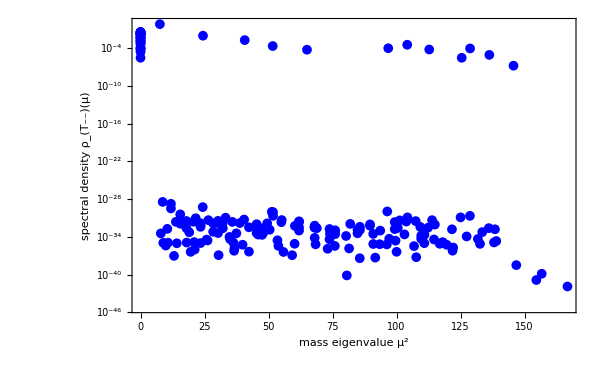

```mathematica
stressTensorDensityPlotN3D9=Block[{dmax=9,density},density=Thread[
{bigInt[dmax]/3//N//Eigenvalues//Reverse,
((bigInt[dmax]/3//N//Eigenvectors//Reverse)[[;;,cut[dmax][1]]].basis[dmax][1])[[;;,2]]//(#^2)&
}];
ListLogPlot[
density,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{"mass eigenvalue  μ^2","spectral density  ρ_(T_(--))(μ)"//TraditionalForm},
LabelStyle->{FontFamily->"Times New Roman",16},
ImageSize->600,
PlotStyle->Blue,
PlotMarkers->{"●",10}
(*Epilog->{ Inset[Text[Style[" N = 3",FontFamily->"Times New Roman",20]],
Scaled[{.8,.8}] ] }*)
]
]
```

#### d7

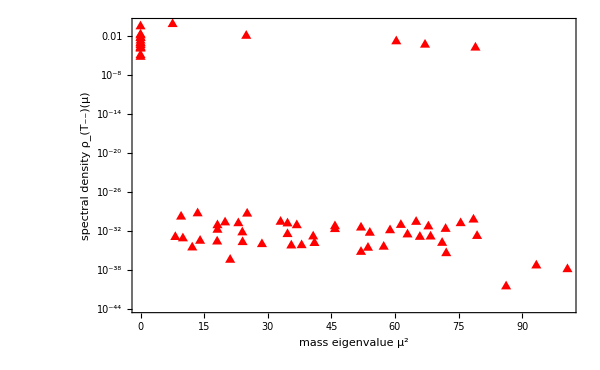

```mathematica
stressTensorDensityPlotN3D7=Block[{dmax=7,density},density=Thread[
{bigInt[dmax]/3//N//Eigenvalues//Reverse,
((bigInt[dmax]/3//N//Eigenvectors//Reverse)[[;;,cut[dmax][1]]].basis[dmax][1])[[;;,2]]//(#^2)&
}];
ListLogPlot[
density,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{"mass eigenvalue  μ^2","spectral density  ρ_(T_(--))(μ)"//TraditionalForm},
LabelStyle->{FontFamily->"Times New Roman",16},
ImageSize->600,
PlotStyle->Red,
PlotMarkers->{"▲",12}
(*Epilog->{ Inset[Text[Style[" N = 3",FontFamily->"Times New Roman",20]],
Scaled[{.8,.8}] ] }*)
]
]
```

#### d5

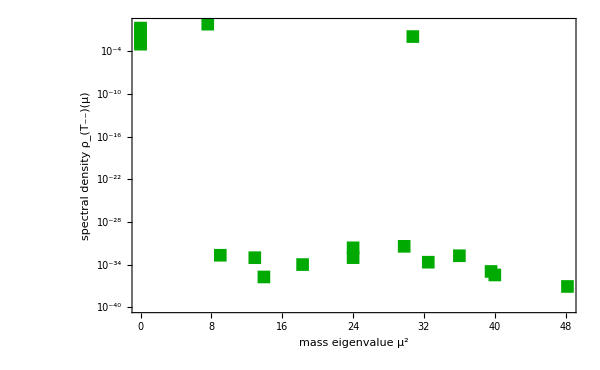

```mathematica
stressTensorDensityPlotN3D5=Block[{dmax=5,density},density=Thread[
{bigInt[dmax]/3//N//Eigenvalues//Reverse,
((bigInt[dmax]/3//N//Eigenvectors//Reverse)[[;;,cut[dmax][1]]].basis[dmax][1])[[;;,2]]//(#^2)&
}];
ListLogPlot[
density,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black],
FrameLabel->{"mass eigenvalue  μ^2","spectral density  ρ_(T_(--))(μ)"//TraditionalForm},
LabelStyle->{FontFamily->"Times New Roman",16},
ImageSize->600,
PlotStyle->Darker[Green],
PlotMarkers->{"■",13}
(*Epilog->{ Inset[Text[Style[" N = 3",FontFamily->"Times New Roman",20]],
Scaled[{.8,.8}] ] }*)
]
]
```

#### collection

```mathematica
lg=PointLegend[
{Blue,Red,Darker[Green]},
{"Δ_max=9","Δ_max=7","Δ_max=5"},
LegendMarkers->{{"●",10},{"▲",12},{"■",13}},
LabelStyle->{FontFamily->"Times New Roman",16}
]
```

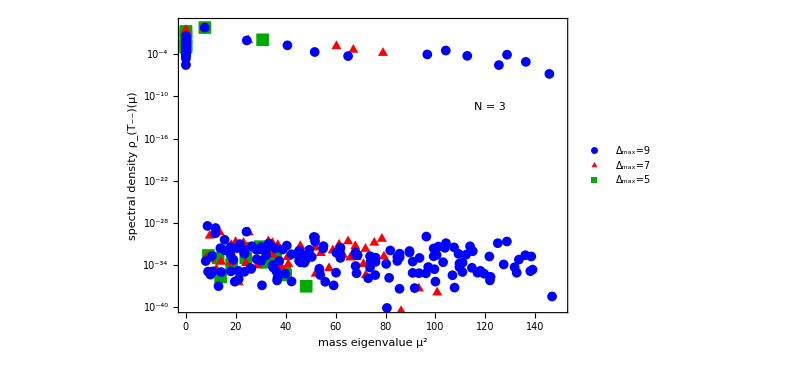

```mathematica
stressTensorDensityPlotN3=Show[
stressTensorDensityPlotN3D5,
stressTensorDensityPlotN3D7,
stressTensorDensityPlotN3D9,
PlotRange->{{0,150},{10^-40,2}//Log},
Epilog->{ 
Inset[Text[Style[" N = 3",FontFamily->"Times New Roman",20]],
Scaled[{.8,.7}] ] ,
Inset[lg,
Scaled[{.8,.5}] ] 
}
]
```

## Use the spectral density to extract the low energy single particle spectrum

## N = 3

Generating the Δmax=9 Nc=3 basis and matrix elements takes 2 hours.
We will skip that step and load the prepared data.

```mathematica
(*ClearAll["Global`*"]*)
(*SetDirectory[NotebookDirectory[]]*)
(*Nc=3;*)
(*Δmax=9;*)
(*Get["QCD-public.wl"]*)
```

```mathematica
(* Load the output file *)
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"QCD_N3_D9"];
```

### Parsing the basis and matrix elements data

```mathematica
PrimCoeffs[ΔA_, ΔB_, l_, k_] = ((-1)^
   k Gamma[2 ΔA + l] Gamma[2 ΔB + l])/(
  k! (l - k)! Gamma[2 ΔA + k] Gamma[
    2 ΔB + l - k]);
```

```mathematica
ClearAll[cut];
cut[Δmax_]:=cut[Δmax]=DeleteCases[
(Position[#,{__,dim_}/;dim≤Δmax,1,Heads->False]//Flatten)&/@primaries,
{}]
```

```mathematica
ClearAll[basis];
basis[dmax_]:=basis[dmax]=DeleteCases[{}]@Association@Table[
nPairs->Block[
{ortho},
ortho=Orthogonalize[
IdentityMatrix[Length[cut[dmax][nPairs]]],
#1.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].#2&
];
ortho[[ Flatten[Position[
ortho.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].ConjugateTranspose[ ortho ]//Diagonal,
_?Positive,1,Heads->False
] ] ]]
],{nPairs,cut[dmax]//Length}]
```

```mathematica
ClearAll[bigInt]
bigInt[Δmax_]:=bigInt[Δmax]=Block[
{basis=basis[Δmax],cut=cut[Δmax]},
ArrayFlatten[
ReplacePart[
ConstantArray[0,{Length[basis],Length[basis]}],
{
{i_,i_}:>basis[i].NtoNMatrices[i][[cut[i],cut[i]]].Transpose[basis[i]],
{i_,j_}/;j==i+1:>basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]],
{j_,i_}/;j==i+1:>Transpose[basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]]]
}
]
]
];
```

```mathematica
singleParticleSpectrum[dmax_]:=Block[
{raw},
raw=Thread[
{bigInt[dmax]/3//N//Eigenvalues//Reverse,
((bigInt[dmax]/3//N//Eigenvectors//Reverse)[[;;,cut[dmax][1]]].basis[dmax][1])[[;;,2]]//(#^2)&
}]//Chop;
{dmax,#}&/@PadRight[
TakeLargestBy[Select[
DeleteCases[{_,0}|{0,_}]@raw,
#[[1]]*2<150&
],Last,UpTo[4]][[;;,1]],
4,na]
]
```

### make plots

```mathematica
d3SingleAntiSymParticleSpectrum=singleParticleSpectrum/@Range[3,9]
```

{{{3,8.},{3,na},{3,na},{3,na}},{{4,7.58963},{4,30.7437},{4,na},{4,na}},{{5,7.58963},{5,30.7437},{5,na},{5,na}},{{6,7.56201},{6,24.9327},{6,60.3202},{6,67.0983}},{{7,7.56201},{7,24.9327},{7,60.3202},{7,67.0983}},{{8,7.55419},{8,24.4208},{8,40.8622},{8,53.9739}},{{9,7.55418},{9,24.3931},{9,40.6803},{9,51.6121}}}

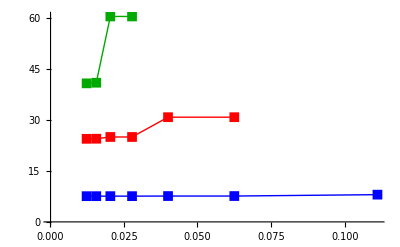

```mathematica
pltd3=ListPlot[
MapAt[1/#^2&,DeleteCases[{_,na}]/@Transpose[d3SingleAntiSymParticleSpectrum],{All,All,1}][[;;3]],
PlotRange->{{0.0001,Automatic},{0,Automatic}},
Joined->True,
PlotMarkers->{"■",10},
PlotStyle->(
Directive[Thick,#]&/@{Blue,Red,Darker[Green]}
)
]
```

## N = 6

Generating the Δmax=9 N=6 basis and matrix elements takes 6 hours.
We will skip that step and load the prepared data.

```mathematica
(*ClearAll["Global`*"]*)
(*SetDirectory[NotebookDirectory[]]*)
(*Nc=6;*)
(*Δmax=9;*)
(*Get["QCD-public.wl"]*)
```

```mathematica
(* Load the output file, this will override the N=3 data *)
Get[NotebookDirectory[]<>"QCD_N6_D9"];
```

### Parsing the basis and matrix elements data

```mathematica
PrimCoeffs[ΔA_, ΔB_, l_, k_] = ((-1)^
   k Gamma[2 ΔA + l] Gamma[2 ΔB + l])/(
  k! (l - k)! Gamma[2 ΔA + k] Gamma[
    2 ΔB + l - k]);
```

```mathematica
ClearAll[cut];
cut[Δmax_]:=cut[Δmax]=DeleteCases[
(Position[#,{__,dim_}/;dim≤Δmax,1,Heads->False]//Flatten)&/@primaries,
{}]
```

```mathematica
ClearAll[basis];
basis[dmax_]:=basis[dmax]=DeleteCases[{}]@Association@Table[
nPairs->Block[
{ortho},
ortho=Orthogonalize[
IdentityMatrix[Length[cut[dmax][nPairs]]],
#1.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].#2&
];
ortho[[ Flatten[Position[
ortho.gramMatrices[nPairs][[cut[dmax][nPairs],cut[dmax][nPairs]]].ConjugateTranspose[ ortho ]//Diagonal,
_?Positive,1,Heads->False
] ] ]]
],{nPairs,cut[dmax]//Length}]
```

```mathematica
ClearAll[bigInt]
bigInt[Δmax_]:=bigInt[Δmax]=Block[
{basis=basis[Δmax],cut=cut[Δmax]},
ArrayFlatten[
ReplacePart[
ConstantArray[0,{Length[basis],Length[basis]}],
{
{i_,i_}:>basis[i].NtoNMatrices[i][[cut[i],cut[i]]].Transpose[basis[i]],
{i_,j_}/;j==i+1:>basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]],
{j_,i_}/;j==i+1:>Transpose[basis[i].NtoN2Matrices[i][[cut[i],cut[j]]].Transpose[basis[j]]]
}
]
]
];
```

```mathematica
singleParticleSpectrum[dmax_]:=Block[
{raw},
raw=Thread[
{bigInt[dmax]/6//N//Eigenvalues//Reverse,
((bigInt[dmax]/6//N//Eigenvectors//Reverse)[[;;,cut[dmax][1]]].basis[dmax][1])[[;;,2]]//(#^2)&
}]//Chop;
{dmax,#}&/@PadRight[
TakeLargestBy[Select[
DeleteCases[{_,0}|{0,_}]@raw,
#[[1]]*2<150&
],Last,UpTo[4]][[;;,1]],
4,na]
]
```

### make plots

```mathematica
d6SingleAntiSymParticleSpectrum=singleParticleSpectrum/@Range[3,9]
```

{{{3,7.},{3,na},{3,na},{3,na}},{{4,6.74386},{4,28.2561},{4,na},{4,na}},{{5,6.74386},{5,28.2561},{5,na},{5,na}},{{6,6.7296},{6,23.8756},{6,53.4425},{6,60.2145}},{{7,6.7296},{7,23.8751},{7,53.4383},{7,60.1853}},{{8,6.7253},{8,23.4816},{8,37.609},{8,47.6373}},{{9,6.72529},{9,23.4641},{9,37.2365},{9,46.5833}}}

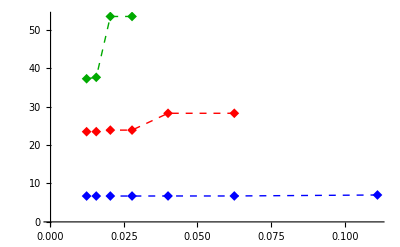

```mathematica
pltd6=ListPlot[
MapAt[1/#^2&,DeleteCases[{_,na}]/@Transpose[d6SingleAntiSymParticleSpectrum],{All,All,1}][[;;3]],
PlotRange->{{0.0001,Automatic},{0,Automatic}},
Joined->True,
PlotMarkers->{"◆",10},
PlotStyle->(
Directive[Thick,Dashed,#]&/@{Blue,Red,Darker[Green]}
)
]
```

## Combine N=3 and N=6 (Fig. 10)

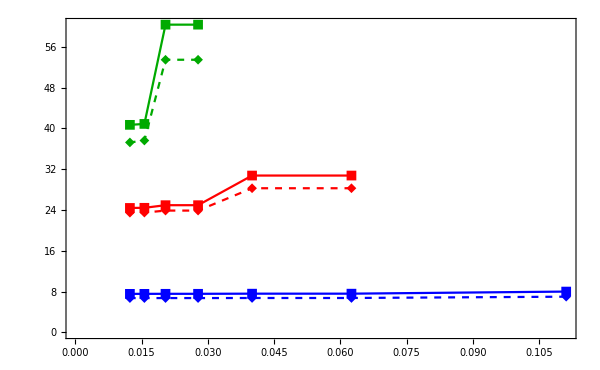
-Graphics-1/Δ_max^2mass eigenvalue μ^2

```mathematica
pltN6AndN3=Labeled[Show[
pltd3,pltd6,
ImageSize->600,
Frame->True,
FrameStyle->Black,
(*FrameLabel->{"1/Δ_max^2","M^2"},*)
LabelStyle->{FontFamily->"Times New Roman",FontSize->16}
],
{"1/Δ_max^2",Rotate["mass eigenvalue μ^2",90Degree]},{Bottom,Left},
LabelStyle->{FontFamily->"Times New Roman",FontSize->20}
]
```